```mathematica
ClearAll["Global`*"]
```

```mathematica
(*This is the code to perform calculations for LESCO. The calculations can be found in "superconductivity.overleaf/The Non-Linear Approach.tex/sec.LESCO/subsection.Determining the Deformation Gradient Geometrically"*)
```

```mathematica
(*Setting up the Canonical basis vectors*)
e1:={1,0,0}
e2:={0,1,0}
e3:={0,0,1}
```

```mathematica
(*Determining the Wells*)
FII:={{a/Subscript[a, 0]*TrigExpand[Cos[Pi/4-β/2]],a/Subscript[a, 0]*TrigExpand[Cos[Pi/4+β/2]],0},{a/Subscript[a, 0]*TrigExpand[Sin[Pi/4-β/2]],a/Subscript[a, 0]*TrigExpand[Sin[Pi/4+β/2]],0},{0,0,c/Subscript[c, 0]}}
Print["F_II=",FII//Simplify//MatrixForm]
FI:={{a/Subscript[a, 0]*TrigExpand[Cos[Pi/4-β/2]],-a/Subscript[a, 0]*TrigExpand[Cos[Pi/4+β/2]],0},{-a/Subscript[a, 0]*TrigExpand[Sin[Pi/4-β/2]],a/Subscript[a, 0]*TrigExpand[Sin[Pi/4+β/2]],0},{0,0,c/Subscript[c, 0]}}
Print["F_I=",FI//Simplify//MatrixForm]
UII:={{a/Subscript[a, 0]*(Sqrt[1-Cos[β]]+Sqrt[1+Cos[β]])/2,a/Subscript[a, 0]*(-Sqrt[1-Cos[β]]+Sqrt[1+Cos[β]])/2,0},{a/Subscript[a, 0]*(-Sqrt[1-Cos[β]]+Sqrt[1+Cos[β]])/2,a/Subscript[a, 0]*(Sqrt[1-Cos[β]]+Sqrt[1+Cos[β]])/2,0},{0,0,c/Subscript[c, 0]}};
Print["U_II=(F_II^T F_II)^(1/2)=",Simplify[MatrixPower[Transpose[FII].FII,1/2],{a>0,Subscript[a, 0]>0,c>0,Subscript[c, 0]>0}]//MatrixForm]
UI:={{a/Subscript[a, 0]*(Sqrt[1-Cos[β]]+Sqrt[1+Cos[β]])/2,a/Subscript[a, 0]*(Sqrt[1-Cos[β]]-Sqrt[1+Cos[β]])/2,0},{a/Subscript[a, 0]*(Sqrt[1-Cos[β]]-Sqrt[1+Cos[β]])/2,a/Subscript[a, 0]*(Sqrt[1-Cos[β]]+Sqrt[1+Cos[β]])/2,0},{0,0,c/Subscript[c, 0]}};
Print["U_I=(F_I^T F_I)^(1/2)=",Simplify[MatrixPower[Transpose[FI].FI,1/2],{a>0,Subscript[a, 0]>0,c>0,Subscript[c, 0]>0}]//MatrixForm]
Transpose[FI]//MatrixForm
```

F_II=(0.16496 a Cos[β/2]+0.16496 a Sin[β/2] | 0.16496 a Cos[β/2]-0.16496 a Sin[β/2] | 0
0.16496 a Cos[β/2]-0.16496 a Sin[β/2] | 0.16496 a Cos[β/2]+0.16496 a Sin[β/2] | 0
0 | 0 | c/c_0)

F_I=(0.16496 a Cos[β/2]+0.16496 a Sin[β/2] | -0.16496 a Cos[β/2]+0.16496 a Sin[β/2] | 0
-0.16496 a Cos[β/2]+0.16496 a Sin[β/2] | 0.16496 a Cos[β/2]+0.16496 a Sin[β/2] | 0
0 | 0 | c/c_0)

U_II=(F_II^T F_II)^(1/2)=(a (0.116644 √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))+0.116644 √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))) | -(0.116644 a (1. √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))-1. √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))) √(1. Cos[0.5 β]^4+1. Sin[0.5 β]^4-0.5 Sin[1. β]^2))/(1. Cos[0.5 β]^2-1. Sin[0.5 β]^2) | 0.
-(0.116644 a (1. Cos[0.5 β]-1. Sin[0.5 β]) (1. Cos[0.5 β]+1. Sin[0.5 β]) (1. √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))-1. √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))))/(√(1. Cos[0.5 β]^4+1. Sin[0.5 β]^4-0.5 Sin[1. β]^2)) | a (0.116644 √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))+0.116644 √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))) | 0.
0. | 0. | (1. c)/c_0)

U_I=(F_I^T F_I)^(1/2)=(a (0.116644 √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))+0.116644 √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))) | (0.116644 a (1. √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))-1. √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))) √(1. Cos[0.5 β]^4+1. Sin[0.5 β]^4-0.5 Sin[1. β]^2))/(1. Cos[0.5 β]^2-1. Sin[0.5 β]^2) | 0.
(0.116644 a (1. Cos[0.5 β]-1. Sin[0.5 β]) (1. Cos[0.5 β]+1. Sin[0.5 β]) (1. √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))-1. √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))))/(√(1. Cos[0.5 β]^4+1. Sin[0.5 β]^4-0.5 Sin[1. β]^2)) | a (0.116644 √(1.-1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))+0.116644 √(1.+1. √(1. Cos[(0.5+0. ⅈ) β]^4-2. Cos[(0.5+0. ⅈ) β]^2 Sin[(0.5+0. ⅈ) β]^2+1. Sin[(0.5+0. ⅈ) β]^4))) | 0.
0. | 0. | (1. c)/c_0)

(0.233288 a (Cos[β/2]/(√2)+Sin[β/2]/(√2)) | -0.233288 a (Cos[β/2]/(√2)-Sin[β/2]/(√2)) | 0
-0.233288 a (Cos[β/2]/(√2)-Sin[β/2]/(√2)) | 0.233288 a (Cos[β/2]/(√2)+Sin[β/2]/(√2)) | 0
0 | 0 | c/c_0)

```mathematica
QI:=FI.Inverse[UI](*The Corresponding Rotations QI*)
QII:=FII.Inverse[UII](*The Corresponding Rotations QII*)
(*Print["F_I=",FI//MatrixForm]
Print["F_II=",FII//MatrixForm]*)
(*Always check if its a rotation.*)
Print["U_I=",UI//MatrixForm]
Print["U_II=",UII//MatrixForm]
Print["Q_I=",Simplify[QI//MatrixForm]]
Print["Q_II=",Simplify[QII//MatrixForm]]
Print["Q_I^T.Q_I=",Transpose[QI].QI//Simplify//PowerExpand//MatrixForm]
Print["Q_II^T.Q_II=",Transpose[QII].QII//Simplify//PowerExpand//MatrixForm]
FI-Transpose[FI]//Simplify//MatrixForm
```

U_I=(0.116644 a (√(1-Cos[β])+√(1+Cos[β])) | 0.116644 a (√(1-Cos[β])-√(1+Cos[β])) | 0
0.116644 a (√(1-Cos[β])-√(1+Cos[β])) | 0.116644 a (√(1-Cos[β])+√(1+Cos[β])) | 0
0 | 0 | c/c_0)

U_II=(0.116644 a (√(1-Cos[β])+√(1+Cos[β])) | 0.116644 a (-√(1-Cos[β])+√(1+Cos[β])) | 0
0.116644 a (-√(1-Cos[β])+√(1+Cos[β])) | 0.116644 a (√(1-Cos[β])+√(1+Cos[β])) | 0
0 | 0 | c/c_0)

Q_I=((0.707107 Cos[β/2] √(1-Cos[β])+0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | (-0.707107 Cos[β/2] √(1-Cos[β])+0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | 0.
(-0.707107 Cos[β/2] √(1-Cos[β])+0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | (0.707107 Cos[β/2] √(1-Cos[β])+0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | 0.
0. | 0. | 1.)

Q_II=((0.707107 Cos[β/2] √(1-Cos[β])+0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | (0.707107 Cos[β/2] √(1-Cos[β])-0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | 0.
(0.707107 Cos[β/2] √(1-Cos[β])-0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | (0.707107 Cos[β/2] √(1-Cos[β])+0.707107 √(1+Cos[β]) Sin[β/2])/(√(Sin[β]^2)) | 0.
0. | 0. | 1.)

Q_I^T.Q_I=(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

Q_II^T.Q_II=(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(0. | 0. | 0
0. | 0. | 0
0 | 0 | 0)

```mathematica
(*Checking if its actually the polar decomposition F^TF-U^2*)
Transpose[FI].FI-UI.UI//Simplify
Transpose[FII].FII-UII.UII//Simplify
FI-QI.UI//Simplify
FII-QII.UII//Simplify
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0}}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0}}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
(*Checking for Twins C=FII^-T FI^T FI FII^-1*)
Inverse[Transpose[FII]].Transpose[FI].FI.Inverse[FII]//Simplify//MatrixForm
Inverse[Transpose[UII]].Transpose[UI].UI.Inverse[UII]//Simplify//MatrixForm
(*Check that the above are equal to "-{{(1 + SuperscriptBox[Cos[β], 2])/Sin[β]^2,-2Cos[β]/Sin[β]^2,0},{-2Cos[β]/Sin[β]^2,(1 + SuperscriptBox[Cos[β], 2])/Sin[β]^2,0},{0,0,1}}" by substracting them and getting 0.*)
Eigensystem[Inverse[Transpose[UII]].Transpose[UI].UI.Inverse[UII]]//Simplify
Inverse[Transpose[UII]].Transpose[UI].UI.Inverse[UII].{-1/4 (1-4 Cos[β]-2 Cos[β]^2+Cos[2 β]) Sec[β],1,0}-((3-4 Cos[β]+Cos[2 β])/(2 (1-Cos[β]) (1+Cos[β])))*{-1/4 (1-4 Cos[β]-2 Cos[β]^2+Cos[2 β]) Sec[β],1,0}//Simplify(*Checking the seoncd eigen vlaue and vector pair*)
Inverse[Transpose[UII]].Transpose[UI].UI.Inverse[UII].{-1/4 (1+4 Cos[β]-2 Cos[β]^2+Cos[2 β]) Sec[β],1,0}-((3+4 Cos[β]+Cos[2 β])/(2 (1-Cos[β]) (1+Cos[β])))*{-1/4 (1+4 Cos[β]-2 Cos[β]^2+Cos[2 β]) Sec[β],1,0}//Simplify(*Checking the third eigen vlaue and vector pair*)
```

(0.5 Cot[β/2]^2+0.5 Tan[β/2]^2 | -0.5 Cot[β/2]^2+0.5 Tan[β/2]^2 | 0
-0.5 Cot[β/2]^2+0.5 Tan[β/2]^2 | 0.5 Cot[β/2]^2+0.5 Tan[β/2]^2 | 0
0. | 0. | 1.)

((-1.-1. Cos[β]^2)/(-1.+Cos[β]^2) | (2. Cos[β])/(-1.+Cos[β]^2) | 0.
(2. Cos[β])/(-1.+Cos[β]^2) | (-1.-1. Cos[β]^2)/(-1.+Cos[β]^2) | 0.
0. | 0. | 1.)

{{1.,-(1. (1.-1. Cos[β])^2)/(-1.+Cos[β]^2),-(1. (1.+1. Cos[β])^2)/(-1.+Cos[β]^2)},{{0,0,1.},{1.,1.,0},{-1.,1.,0}}}

{0.,0.,0.}

{0.,0.,0.}

```mathematica
Sin[3*Pi/4]
```

1/(√2)

```mathematica
Simplify[-1/4 (1-4 Cos[β]-2 Cos[β]^2+Cos[2 β]) Sec[β]]
```

1

```mathematica
(*Clausius clayperon equation for Subscript[σ, 110]*)
A:=TensorProduct[(e1+e2)/Sqrt[2],(e1+e2)/Sqrt[2]](*direction of the load*)
Q:={{Cos[θ]+Subscript[u, x]^2*(1-Cos[θ]) , Subscript[u, x]*Subscript[u, y]*(1-Cos[θ])-Subscript[u, z]*Sin[θ] , Subscript[u, x]*Subscript[u, z]*(1-Cos[θ])+Subscript[u, y]*Sin[θ]},{ Subscript[u, x]*Subscript[u, y]*(1-Cos[θ])+Subscript[u, z]*Sin[θ] ,Cos[θ]+Subscript[u, y]^2*(1-Cos[θ]) , Subscript[u, y]*Subscript[u, z]*(1-Cos[θ])-Subscript[u, x]*Sin[θ]},{ Subscript[u, x]*Subscript[u, z]*(1-Cos[θ])-Subscript[u, y]*Sin[θ] , Subscript[u, y]*Subscript[u, z]*(1-Cos[θ])+Subscript[u, x]*Sin[θ] ,Cos[θ]+Subscript[u, z]^2*(1-Cos[θ])}}(*This is the general expression of a tensor in SO(3). It rotates all objects about the axis u by an angle θ*)
A//MatrixForm
Q//MatrixForm
(*Determining the touching point for Subscript[σ, 110] for the Austenite phase*)
Temp=Tr[Transpose[A].Q]-(Cos[θ]+(1-Cos[θ])/2*(Subscript[u, x]+Subscript[u, y])^2)//Simplify;(*Checking that we have the correct expression for A:Q*)
Print["A:Q-(Cos[θ]+(1 - Cos[θ])/2*(u_x+u_y)^2)=",Temp]
Maximize[{Cos[θ]+(1-Cos[θ])/2*(Subscript[u, x]+Subscript[u, y])^2,0<=Subscript[u, x]^2+Subscript[u, y]^2<=1},{θ,Subscript[u, x],Subscript[u, y]}]
(*Determining the touching point for Subscript[σ, 110] for the MArtensite phase*)
Print["1/2(U_I(e_1/(√2)))^2=",1/2*(UI.((e1+e2)/Sqrt[2])).UI.((e1+e2)/Sqrt[2])//Simplify]
Print["1/2(U_II(e_1/(√2)))^2=",1/2*(UII.((e1+e2)/Sqrt[2])).UII.((e1+e2)/Sqrt[2])//Simplify]
Print["Checking if A*UI==a/a_0*√(1-Cos[β])A,----->",A.UI-a/Subscript[a, 0]*Sqrt[1-Cos[β]]*A//Simplify]
Tr[Q.Transpose[A]]//Simplify
Print["A:(U_I-I)=",Tr[Transpose[A].(UI-IdentityMatrix[3])]//Simplify]
```

(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

(Cos[θ]+(1-Cos[θ]) u_x^2 | (1-Cos[θ]) u_x u_y-Sin[θ] u_z | Sin[θ] u_y+(1-Cos[θ]) u_x u_z
(1-Cos[θ]) u_x u_y+Sin[θ] u_z | Cos[θ]+(1-Cos[θ]) u_y^2 | -Sin[θ] u_x+(1-Cos[θ]) u_y u_z
-Sin[θ] u_y+(1-Cos[θ]) u_x u_z | Sin[θ] u_x+(1-Cos[θ]) u_y u_z | Cos[θ]+(1-Cos[θ]) u_z^2)

A:Q-(Cos[θ]+(1 - Cos[θ])/2*(u_x+u_y)^2)=0

{1,{θ→0,u_x→-27/32,u_y→0}}

1/2(U_I(e_1/(√2)))^2=-0.0272116 a^2 (-1.+Cos[β])

1/2(U_II(e_1/(√2)))^2=0.0272116 a^2 (1.+Cos[β])

Checking if A*UI==a/a_0*√(1-Cos[β])A,----->{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

Cos[θ]+Sin[θ/2]^2 u_x^2+2 Sin[θ/2]^2 u_x u_y+Sin[θ/2]^2 u_y^2

A:(U_I-I)=-1.+0.233288 a √(1-Cos[β])

```mathematica
(*Clausius clayperon equation for Subscript[σ, 100]*)
Print["U_Ie_1=",UI.e1//Simplify//MatrixForm]
Print["(U_Ie_1)^2=",(UI.e1).(UI.e1)//Simplify]
Print["U_IIe_1=",UII.e1//Simplify//MatrixForm]
Print["(U_IIe_1)^2=",(UII.e1).(UII.e1)//Simplify]
Print["Unit vector along U_Ie_1 is ---->OverHat[(SubscriptBox[U, I] SubscriptBox[e, 1])=]",Simplify[(UI.e1)/Sqrt[(UI.e1).(UI.e1)],{a>0,Subscript[a, 0]>0}]]
q1:=Simplify[(UI.e1)/Sqrt[(UI.e1).(UI.e1)],{a>0,Subscript[a, 0]>0}]
q2:=Cross[e3,q1]
Print["q1=",q1//Simplify//MatrixForm]
Print["q2=",q2//Simplify//MatrixForm]
Subscript[Q, 100]:={q1,q2,e3}
Print["Q_100=",Subscript[Q, 100]//MatrixForm//Simplify]
Print["Checking Orthogonality of Q_100 ,ie, Q_100.Q_100^T==I--->",Subscript[Q, 100].Transpose[Subscript[Q, 100]]//MatrixForm//Simplify]
Print["F_M=Q_100U_I=",Subscript[Q, 100]*UI//MatrixForm//Simplify](*-({{(a (1+Sin[β]))/(2 Subscript[a, 0]), -(a (-1+Sin[β]))/(2 Subscript[a, 0]), 0}, {(a (-1+Sin[β]))/(2 Subscript[a, 0]), (a (1+Sin[β]))/(2 Subscript[a, 0]), 0}, {0, 0, c/Subscript[c, 0]}})*)
```

U_Ie_1=(0.116644 a (√(1-Cos[β])+√(1+Cos[β]))
0.116644 a (√(1-Cos[β])-1. √(1+Cos[β]))
0)

(U_Ie_1)^2=0.0544233 a^2

U_IIe_1=(0.116644 a (√(1-Cos[β])+√(1+Cos[β]))
-0.116644 a (√(1-Cos[β])-1. √(1+Cos[β]))
0)

(U_IIe_1)^2=0.0544233 a^2

Unit vector along U_Ie_1 is ---->OverHat[(SubscriptBox[U, I] SubscriptBox[e, 1])=]{0.5 (√(1-Cos[β])+√(1+Cos[β])),0.5 (√(1-Cos[β])-1. √(1+Cos[β])),0}

q1=(0.5 (√(1-Cos[β])+√(1+Cos[β]))
0.5 (√(1-Cos[β])-1. √(1+Cos[β]))
0)

q2=(-0.5 √(1-Cos[β])+0.5 √(1+Cos[β])
0.5 √(1-Cos[β])+0.5 √(1+Cos[β])
0.)

Q_100=(0.5 (√(1-Cos[β])+√(1+Cos[β])) | 0.5 (√(1-Cos[β])-1. √(1+Cos[β])) | 0
-0.5 √(1-Cos[β])+0.5 √(1+Cos[β]) | 0.5 √(1-Cos[β])+0.5 √(1+Cos[β]) | 0.
0 | 0 | 1)

Checking Orthogonality of Q_100 ,ie, Q_100.Q_100^T==I--->(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1)

F_M=Q_100U_I=(0.058322 a (√(1-Cos[β])+√(1+Cos[β]))^2 | a (0.116644-0.116644 √(Sin[β]^2)) | 0
a (-0.116644+0.116644 √(Sin[β]^2)) | 0.058322 a (√(1-Cos[β])+√(1+Cos[β]))^2 | 0.
0 | 0 | c/c_0)

```mathematica
(*Solving the System of equations*)
(*a/Subscript[a, 0] is abbreviated as x. β is replaced by b and Subscript[η, M]-Subscript[η, A] is replaced by n*)
K1:=-0.3785*10^8
K2:=1.19695*10^8
K3:=1.53824*10^8
Eqns1[n_,Subscript[a, p]_,b_]:=n-K1*(Subscript[a, p]*Sqrt[2]*Sin[b/2]-1)
Eqns2[n_,Subscript[a, p]_,b_]:=n+K2*(1/Subscript[a, p]^2*1/Sin[b]-1)
Eqns3[n_,Subscript[a, p]_,b_]:=n-K3*(Subscript[a, p]*(1+Sin[b])/2-1)
NSolve[z-K1*(x*Sqrt[1-Cos[y]]-1)==0&&z+K2*(1/x^2*1/Sin[y]-1)==0&&z-K3*(x*(1+Sin[y])/2-1)==0&&0<=y<=2*Pi,{x,y,z},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.,y→1.5708,z→7.45058×10^-9},{x→1.32638,y→0.696369,z→1.3626×10^7}}

```mathematica
-16218.732487944388-K1*(1.3213696495211946*Sqrt[2]*Sin[0.6125456040075239/2]-1)
```

-1.65406×10^7

```mathematica
1.5707963267948966-Pi/2
```

0.

```mathematica
(*Extracting the Stress vs Strain data for LESCO*)
(*-Graphics- The units are in K and Kbar=10^8 Pa*)
```

```mathematica
P110={{-0.0846182853784988,9.89492119089317},{-0.5595319342875719,11.120840630472856},{-0.9816424405490377,12.276707530647986},{-1.540952279599396,13.782837127845884},{-2.089749610754962,15.183887915936953},{-2.5224466566569577,16.30472854640981},{-2.9234581153831027,17.390542907180386}};
P100={{-0.05341390454994477,8.949211908931698},{-0.4548510458140832,9.229422066549912},{-0.7822934572131212,9.544658493870402},{-1.1625760271326349,9.859894921190893},{-1.9759443096192686,10.560420315236426},{-2.979444623097442,11.436077057793344}};
P001={{-0.011308349161474829,8.633975481611207},{-0.2544471101014002,8.493870402802102},{-0.48701783933723075,8.353765323992993},{-0.8993006313519817,8.108581436077058},{-1.4384738355616116,7.723292469352012},{-1.988196563538903,7.373029772329247},{-2.728217893935643,6.882661996497372},{-2.9713751628120035,6.70753064798599},{-3.425967097516003,6.392294220665498},{-3.7325510645533684,6.182136602451838}};
P110[[1,2]]
Sclng:=10^8(*to convert Kbar to Pascal*)
P110[[;;,1]]=Sclng*P110[[;;,1]];
P110
P100[[;;,1]]=Sclng*P100[[;;,1]];
P100
P001[[;;,1]]=Sclng*P001[[;;,1]];
P001
```

9.89492

{{-8.46183×10^6,9.89492},{-5.59532×10^7,11.1208},{-9.81642×10^7,12.2767},{-1.54095×10^8,13.7828},{-2.08975×10^8,15.1839},{-2.52245×10^8,16.3047},{-2.92346×10^8,17.3905}}

{{-5.34139×10^6,8.94921},{-4.54851×10^7,9.22942},{-7.82293×10^7,9.54466},{-1.16258×10^8,9.85989},{-1.97594×10^8,10.5604},{-2.97944×10^8,11.4361}}

{{-1.13083×10^6,8.63398},{-2.54447×10^7,8.49387},{-4.87018×10^7,8.35377},{-8.99301×10^7,8.10858},{-1.43847×10^8,7.72329},{-1.9882×10^8,7.37303},{-2.72822×10^8,6.88266},{-2.97138×10^8,6.70753},{-3.42597×10^8,6.39229},{-3.73255×10^8,6.18214}}

9.7-2.642×10^-8 P

-3.78501×10^7

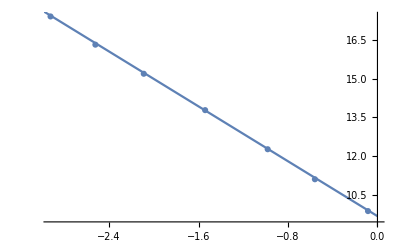

8.9-8.35454×10^-9 P

-1.19695×10^8

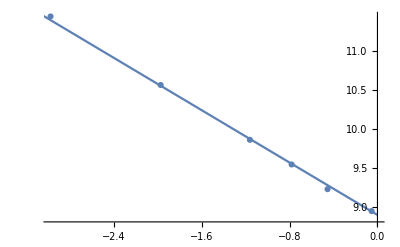

8.65+6.50092×10^-9 P

1.53824×10^8

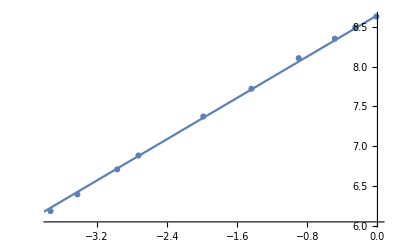

```mathematica
dP110bdT=Table[((P110[[i,1]]-P110[[i+1,1]])/(P110[[i,2]]-P110[[i+1,2]])),{i,1,Length[P110]-1}];
T110[P_]:=9.7+(Total[dP110bdT]/Length[dP110bdT])^-1*P
T110[P]
Total[dP110bdT]/Length[dP110bdT]
p1=ListPlot[P110, PlotMarkers->Automatic];
p2 = Plot[T110[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
dP100bdT=Table[((P100[[i,1]]-P100[[i+1,1]])/(P100[[i,2]]-P100[[i+1,2]])),{i,1,Length[P100]-1}];
T100[P_]:=8.9+(Total[dP100bdT]/Length[dP100bdT])^-1*P
T100[P]
Total[dP100bdT]/Length[dP100bdT]
p1=ListPlot[P100, PlotMarkers->Automatic];
p2 = Plot[T100[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
dP001bdT=Table[((P001[[i,1]]-P001[[i+1,1]])/(P001[[i,2]]-P001[[i+1,2]])),{i,1,Length[P001]-1}];
T001[P_]:=8.65+(Total[dP001bdT]/Length[dP001bdT])^-1*P
T001[P]
Total[dP001bdT]/Length[dP001bdT]
p1=ListPlot[P001, PlotMarkers->Automatic];
p2 = Plot[T001[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
```

```mathematica
(*Solving the System of equations*)
Tidey1[n_,b_]:=n-0.3785*10^8*(5.3225/5.345*Sqrt[2]*Sin[b/2]-1)
Tidey2[n_,b_]:=n-1.19655*10^8*(5.3225/5.345*(1+Sin[b])/2-1)
NSolve[Tidey1[n,b]==0&&Tidey2[n,b]==0&&0<=b<=2*Pi,{n,b},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→-1.67264×10^7,b→0.814956},{n→-514154.,b→1.55206}}

```mathematica
Pi/2-1.5520556893703157
```

0.0187406